```mathematica
Integrate[Exp[I k x-I k^2t/(2m)],{k,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^((ⅈ m x^2)/(2 t)) √(2 π))/(√((ⅈ t)/m)), Im[t/m]<0]

```mathematica
Integrate[Exp[I m x^2/(2t)-I k x],{x,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-(ⅈ k^2 t)/(2 m)) √(2 π))/(√(-(ⅈ m)/t)), Im[m/t]>0]

```mathematica
Integrate[Exp[-I k x+I k^2t/(2m)],{k,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-(ⅈ m x^2)/(2 t)) √(2 π))/(√(-(ⅈ t)/m)), Im[t/m]>0]

```mathematica
Series[(e+s)/(Sqrt[(e+s)^2-s^2])-1,{e,0,2}]
```

```mathematica
Simplify[(√e s)/(√2 √(e s) √e)-1+(3 √e √e)/(4 √2 √(e s))-(5 √e e^(3/2))/(32 (√2 s √(e s)))+O[e]^(5/2),Assumptions->{e>0&&s>0}]
```

(√s)/(√2 √e)-1+(3 √e)/(4 √2 √s)-(5 e^(3/2))/(32 (√2 s^(3/2)))+O[e]^(5/2)

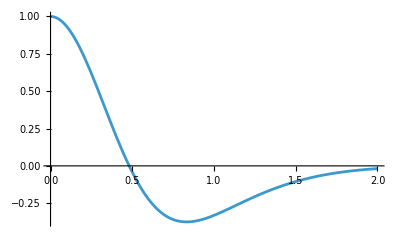

```mathematica
ClearAll[U1,U2,R1,R2]
U1:=2
U2:=1
R1:=2
R2:=1
Plot[U1 Exp[-R1^2k^2]-U2 Exp[-R2^2k^2],{k,0,2}]
ClearAll[U1,U2,R1,R2]
```

```mathematica
Integrate[U Exp[-R^2k^2+I k r],{k,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-r^2/(4 R^2)) √π U)/(√(R^2)), Re[R^2]>0]

```mathematica
(2Pi^2 0.14513/10^3)/(5 238.2^2 (6.646 10^(-27))^2) 1.055 10^(-34)
```

2.41193×10^10

```mathematica
(2Pi^2 0.14513/10^3)/(5 238.2^2 (6.646 10^(-27))^2) 1.055 10^(-34)/31536000
```

764.819

```mathematica
ClearAll[k]
k[n_]:=2Pi n/L
Sum[-I/(2v k[n])Exp[I(-v k[n]t+k[n]x)],{n,1,Infinity}]
Sum[-I/(2v k[n])Exp[I(-v k[n]t-k[n]x)],{n,1,Infinity}]
ClearAll[k]
```

(ⅈ L Log[ⅇ^(-(2 ⅈ π (t v-x))/L) (-1+ⅇ^((2 ⅈ π (t v-x))/L))])/(4 π v)

(ⅈ L Log[ⅇ^(-(2 ⅈ π (t v+x))/L) (-1+ⅇ^((2 ⅈ π (t v+x))/L))])/(4 π v)

```mathematica
Sum[Exp[u n]/n,{n,1,Infinity}]
```

-Log[1-ⅇ^u]

```mathematica
Cos[I u+eps u]
```

Cosh[u-ⅈ eps u]

```mathematica
Simplify[2-2 Cosh[2 u]]
```

-4 Sinh[u]^2

```mathematica
Sum[Exp[s u]/u,{u,1,Infinity}]
```

-Log[1-ⅇ^s]

```mathematica
D[D[Log[v^2t^2-x^2-I eps],t],t]
```

-(4 t^2 v^4)/((-ⅈ eps+t^2 v^2-x^2)^2)+(2 v^2)/(-ⅈ eps+t^2 v^2-x^2)

```mathematica
Simplify[-(4 t^2 v^4)/((-ⅈ eps+t^2 v^2-x^2)^2)+(2 v^2)/(-ⅈ eps+t^2 v^2-x^2)]
```

(2 v^2 (ⅈ eps+t^2 v^2+x^2))/((eps+ⅈ (t^2 v^2-x^2))^2)